```mathematica
(* Tensor product *)
CircleTimes=KroneckerProduct;
```

```mathematica
(* Identity matrix *)
Id=IdentityMatrix[2];
```

```mathematica
(* Projector with angle θ *)
Π[θ_]:=({{Cos[θ]}, {Sin[θ]}}).({{Cos[θ]}, {Sin[θ]}})ᵀ;
(* Alice's measurements *)
A[0,1]=Π[Subscript[α, 0]];
A[0,2]=Id-%;
A[1,0]=Π[Subscript[α, 1]];
A[1,1]=Id-%;
(* Bob's measurements *)
B[0,0]=Π[Subscript[β, 0]];
B[0,1]=Id-%;
B[1,0]=Π[Subscript[β, 1]];
B[1,2]=Id-%;
```

```mathematica
(* Sum of their operators *)
S=1/5 Plus@@{
A[1,0]⊗B[0,0],
A[1,0]⊗B[1,0],
A[0,1]⊗B[0,1],
A[1,1]⊗B[0,1],
A[0,2]⊗B[1,2]}//FullSimplify;
(* Replace Subscript[α, i] and Subscript[β, i] by θ angles *)
tothetas={Subscript[α, 0]->-Subscript[θ, 1],Subscript[α, 1]->Subscript[θ, 2],Subscript[β, 0]->π/2-Subscript[θ, 2],Subscript[β, 1]->Subscript[θ, 1]};
Sθ=S/.tothetas;
```

```mathematica
(* Angles in an optimal strategy *)
θs={Subscript[θ, 1]->1/4 ArcCos[(121+52 √13)/477],Subscript[θ, 2]->1/4 ArcCos[(-431+4 √13)/477]};
```

```mathematica
(* Optimal numerical values of the angles *)
{Subscript[α, 0],Subscript[α, 1],Subscript[β, 0],Subscript[β, 1]}/.tothetas/.θs//N
```

{-0.216878,0.658198,0.912599,0.216878}

```mathematica
(* Optimal shared entangled state *)
v={√(1/2+1/78 √(715-182 √13)),0,0,√(1/2-1/78 √(715-182 √13))};
```

```mathematica
(* Compare a general strategy parameterized by angles Subscript[θ, 1] and Subscript[θ, 2] to the optimal one *)
zs=Sθ.v-opt*v//Simplify;
(* Find an optimal choice of the angles Subscript[θ, 1] and Subscript[θ, 2] up to very high accuracy*)
{val,sol}=FindMinimum[Total[zs^2],{Subscript[θ, 1],Subscript[θ, 2]},WorkingPrecision->1000,MaxIterations->10000];
val
```

1.436810394213091073055479484998719326048210779989444114335049316796923457846319461807332897383504036133080322121691282800495104579144044206749765252904084897574542360427432848758372141042115217140844062959424669319526450452253345821768628516158231655193385931023179719052746272729806022569890038157221846539302664953769477640058389093052550862114531867052529732054857254268717199403375003293842572579910006375495434415358375248871454781627037863131787441671801639475363740975049065434826241094405272817437301507251755327298590223543257325134454604905401694839923025386630812301333321600614703689496804286431364427912511959723456908615720249153860368971061688742940518375506323903719631915793731387160630004755089549205841326256261694772738793919134143690674999754538503169721961456443470860824561787468462020853914668680350512745794290435176465516929052297874845018031812536053103693389993271028441135451203168182806215671844828915923630353135392247377432615731851091160579579559599260664844504025764×10^-1703

```mathematica
(* Find algebraic expressions for the cosines of the angles times 4 *)
ToRadicals@RootApproximant[Cos[4{Subscript[θ, 1],Subscript[θ, 2]}]/.sol]
```

{1/477 (121+52 √13),1/477 (-431+4 √13)}

```mathematica
(* The algebraic numbers look more complicated without the extra factor of 4 *)
ToRadicals@RootApproximant@N[Cos[{Subscript[θ, 1],Subscript[θ, 2]}]/.θs,5000]
```

{√(1/318 (159+√(689 (23+2 √13)))),√(1/318 (159+√(53 (23+2 √13))))}

```mathematica
(* Relationship between the thetas *)
Cos[4 Subscript[θ, 1]]==12+13Cos[4 Subscript[θ, 2]]/.θs
```

True

```mathematica
(* Eigenvalues of the optimal matrix *)
Sθ/.θs;
RootApproximant@Eigenvalues@N[%,1000]
N@%
```

{1/45 (16+√13),1/90 (25+√13),1/45 (7+√13),1/90 (19-5 √13)}

{0.435679,0.317839,0.235679,0.0108027}

```mathematica
(* Find exact algebraic expressions for all matrix entries *)
MatrixForm@RootApproximant[Sθ/.sol]
MatrixForm@Simplify@ToRadicals[%]
%==Sx
```

(Root0.333Root[873729-12571235 #1+67513450 #1^2-160391250 #1^3+142205625 #1^4&,4]0.3328371701075814 | Root-0.0436Root[6561-24684075 #1^2+19200649375 #1^4-4698710859375 #1^6+249659750390625 #1^8&,3]-0.04358700215586275 | Root0.0436Root[6561-24684075 #1^2+19200649375 #1^4-4698710859375 #1^6+249659750390625 #1^8&,6]0.04358700215586275 | (95+29 √13)/1590
Root-0.0436Root[6561-24684075 #1^2+19200649375 #1^4-4698710859375 #1^6+249659750390625 #1^8&,3]-0.04358700215586275 | (520-17 √13)/2385 | (95+29 √13)/1590 | Root0.0532Root[6561-24684075 #1^2+19200649375 #1^4-4698710859375 #1^6+249659750390625 #1^8&,7]0.05319441936909444
Root0.0436Root[6561-24684075 #1^2+19200649375 #1^4-4698710859375 #1^6+249659750390625 #1^8&,6]0.04358700215586275 | (95+29 √13)/1590 | (520-17 √13)/2385 | Root-0.0532Root[6561-24684075 #1^2+19200649375 #1^4-4698710859375 #1^6+249659750390625 #1^8&,2]-0.05319441936909444
(95+29 √13)/1590 | Root0.0532Root[6561-24684075 #1^2+19200649375 #1^4-4698710859375 #1^6+249659750390625 #1^8&,7]0.05319441936909444 | Root-0.0532Root[6561-24684075 #1^2+19200649375 #1^4-4698710859375 #1^6+249659750390625 #1^8&,2]-0.05319441936909444 | Root0.283Root[873729-12571235 #1+67513450 #1^2-160391250 #1^3+142205625 #1^4&,3]0.2825040220793266)

((1345+34 √13+3 √(53 (23+2 √13)))/4770 | -(√(11895-1641 √13-√(106 (1355635-372371 √13))))/1590 | (√(11895-1641 √13-√(106 (1355635-372371 √13))))/1590 | (95+29 √13)/1590
-(√(11895-1641 √13-√(106 (1355635-372371 √13))))/1590 | (520-17 √13)/2385 | (95+29 √13)/1590 | (√(11895-1641 √13+√(106 (1355635-372371 √13))))/1590
(√(11895-1641 √13-√(106 (1355635-372371 √13))))/1590 | (95+29 √13)/1590 | (520-17 √13)/2385 | -(√(11895-1641 √13+√(106 (1355635-372371 √13))))/1590
(95+29 √13)/1590 | (√(11895-1641 √13+√(106 (1355635-372371 √13))))/1590 | -(√(11895-1641 √13+√(106 (1355635-372371 √13))))/1590 | (1345+34 √13-3 √(53 (23+2 √13)))/4770)

True

```mathematica
Sx=1/4770({{1345+34 √13+3 √(53 (23+2 √13)), -3 √(11895-1641 √13-√(106 (1355635-372371 √13))), 3 √(11895-1641 √13-√(106 (1355635-372371 √13))), 285+87 √13}, {-3 √(11895-1641 √13-√(106 (1355635-372371 √13))), 1040-34 √13, 285+87 √13, 3 √(11895-1641 √13+√(106 (1355635-372371 √13)))}, {3 √(11895-1641 √13-√(106 (1355635-372371 √13))), 285+87 √13, 1040-34 √13, -3 √(11895-1641 √13+√(106 (1355635-372371 √13)))}, {285+87 √13, 3 √(11895-1641 √13+√(106 (1355635-372371 √13))), -3 √(11895-1641 √13+√(106 (1355635-372371 √13))), 1345+34 √13-3 √(53 (23+2 √13))}});
```

```mathematica
(* Double check the eigenvalues *)
RootApproximant@Eigenvalues[Sx]
N@%
```

{1/45 (16+√13),1/90 (25+√13),1/45 (7+√13),1/90 (19-5 √13)}

{0.435679,0.317839,0.235679,0.0108027}

```mathematica
(* Compare the two solutions to make sure they agree *)
Sx.v-opt*v//FullSimplify
```

{0,0,0,0}

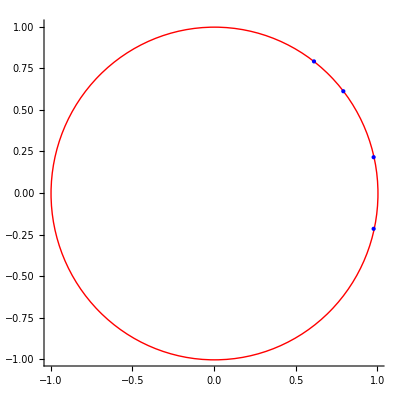

```mathematica
(* Plot the angles on the unit circle *)
({{Cos[Subscript[α, 0]], Cos[Subscript[α, 1]], Cos[Subscript[β, 0]], Cos[Subscript[β, 1]]}, {Sin[Subscript[α, 0]], Sin[Subscript[α, 1]], Sin[Subscript[β, 0]], Sin[Subscript[β, 1]]}})/.tothetas/.θs;
Graphics[{Red,Circle[],Blue,Point/@Transpose[%]},Axes->True]
```

```mathematica
(* Find the polynomial *)
S/.{Subscript[α, 0]->0,Subscript[α, 1]->α/2,Subscript[β, 0]->0,Subscript[β, 1]->π/2-β/2};
Sab=TrigExpand[TrigReduce[%]]/.{Cos[α]->a,Cos[β]->b,Sin[α]->√(1-a^2),Sin[β]->√(1-b^2)};
FullSimplify@CoefficientList[poly=CharacteristicPolynomial[%,t],t]
poly-p//FullSimplify
```

{-((1+a) (-3+a (-1+b)-b) (1+b))/5000,1/500 (-19-3 b-3 a (1+b)),1/100 (33+a+b+a b),-1,1}

0

```mathematica
(* Double check that the coefficients agree *)
CoefficientList[poly,t]-CoefficientList[p,t]//FullSimplify
```

{0,0,0,0,0}

```mathematica
(**************************************************************************)
```

```mathematica
p=1/5000(1+a)(1+b)(4-(1-a)(1-b))-1/500(16+3(1+a)(1+b))t+1/100(32+(1+a)(1+b))t^2-t^3+t^4;
```

```mathematica
opt=(16+√13)/45;
```

```mathematica
cs={1,t-opt,1-a^2,1-b^2};
monoms={1,a,b,a b,t,t^2};
{n,d}=Length/@{cs,monoms};
```

```mathematica
Q={({{α, β, β, γ, δ, ε}, {β, ζ, η, θ, -3/1000, 1/200}, {β, η, ζ, θ, -3/1000, 1/200}, {γ, θ, θ, ι, -3/1000, 1/200}, {δ, -3/1000, -3/1000, -3/1000, κ, -1/2}, {ε, 1/200, 1/200, 1/200, -1/2, 1}}),({{λ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}}),({{μ, 0, θ, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {θ, 0, ν, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}}),({{μ, θ, 0, 0, 0, 0}, {θ, ν, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}})};
{α->(973343+240821 √13)/371790000,β->(33139-617 √13)/82620000,γ->(20-√13)/45000,δ->-(1721+62 √13)/81000,ε->(25-2 √13)/600,ζ->(21592-2903 √13)/185895000,η->(-2+√13)/45000,θ->(-91+617 √13)/82620000,ι->(-47+127 √13)/4590000,κ->(37+√13)/150,λ->(91+31 √13)/20250,μ->(8203-1325 √13)/743580000,ν->(871+127 √13)/9180000};
Q=Q/.%;
```

```mathematica
(* Make sure the polynomial is correct *)
p==Sum[cs⟦k⟧(monoms.Q⟦k⟧.monoms),{k,n}]//FullSimplify
```

True

```mathematica
(* Compute the eigenvalues of Q to make sure it is positive semidefinite *)
MatrixForm[Eigenvalues/@Q]
N[Eigenvalues@Q⟦1⟧,16]
```

((Root9.33 × 10^8Root[{-13+#1^2&,-52998980942502619021670400+12733168976073265754880000 #1+1339254456468146931456 #2-152262039124546937856 #1 #2+1313448755310544 #2^2-4301749925132240 #1 #2^2+928988792 #2^3+5464328 #1 #2^3-#2^4&},{2,4}]9.334832735047401e8)/743580000 | (Root1.52 × 10^7Root[{-13+#1^2&,-52998980942502619021670400+12733168976073265754880000 #1+1339254456468146931456 #2-152262039124546937856 #1 #2+1313448755310544 #2^2-4301749925132240 #1 #2^2+928988792 #2^3+5464328 #1 #2^3-#2^4&},{2,3}]1.5151593078564433e7)/743580000 | (Root4.46 × 10^4Root[{-13+#1^2&,-52998980942502619021670400+12733168976073265754880000 #1+1339254456468146931456 #2-152262039124546937856 #1 #2+1313448755310544 #2^2-4301749925132240 #1 #2^2+928988792 #2^3+5464328 #1 #2^3-#2^4&},{2,2}]44603.31836785571)/743580000 | (14927-3517 √13)/92947500 | (Root1.12 × 10^4Root[{-13+#1^2&,-52998980942502619021670400+12733168976073265754880000 #1+1339254456468146931456 #2-152262039124546937856 #1 #2+1313448755310544 #2^2-4301749925132240 #1 #2^2+928988792 #2^3+5464328 #1 #2^3-#2^4&},{2,1}]11236.88828121984)/743580000 | 0
(91+31 √13)/20250 | 0 | 0 | 0 | 0 | 0
(39377+4481 √13)/371790000 | 0 | 0 | 0 | 0 | 0
(39377+4481 √13)/371790000 | 0 | 0 | 0 | 0 | 0)

{1.255390507416472,0.02037654735006917,0.0000599845589820271,0.00002416714988776621,0.00001511187536138659,0}